## Import paddock data

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

## Brownian Motion Model

```mathematica
paddockMemberQ=RegionMember[paddockRegion];
```

```mathematica
RandomMotion[position_,radius_,steps_]:=NestList[Module[{v},
v=RandomPoint[Circle[#,radius]];
While[!paddockMemberQ[v],v=RandomPoint[Circle[#,radius]]];v]&,
position,steps];
```

```mathematica
example = RandomMotion[RandomPoint[paddockRegion],50,500];
```

```mathematica
nullModelDataSet = Table[RandomMotion[RandomPoint[paddockRegion],50,100],51];
```

```mathematica
Dimensions[nullModelDataSet]
```

{51,101,2}

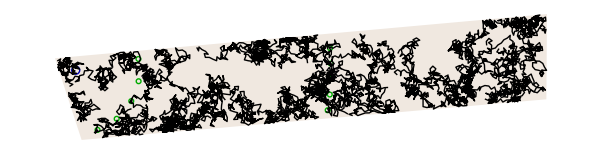

```mathematica
Show[{metadataGraphic,Graphics[Line[nullModelDataSet]]}]
```

```mathematica
dbScanClusters[data_,time_,radius_]:=
Module[{positions,rawClusters,outliers},
positions=DeleteMissing[MapIndexed[#1->#2[[1]]&,data[[All,time]]],1,3];
rawClusters=FindClusters[positions,Method->{"DBSCAN","NeighborhoodRadius"->radius,"DropAnomalousValues"->True},DistanceFunction->EuclideanDistance];
outliers=Complement[Values[positions],Flatten[rawClusters]];
Append[rawClusters,outliers]]
```

```mathematica
nullModelDBSCAN50=DeleteCases[Table[dbScanClusters[nullModelDataSet,x,50],{x,1,Length[nullModelDataSet[[1]]]}],{}];
```

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_]:=Graph[Catenate[Table[FindRulesFromTo[nullModelDBSCAN50[[a]],nullModelDBSCAN50[[a+1]],a,threshold],{a,tmin,tmax}]]]
```

```mathematica
g=FindFissionFusionGraph[1,99,0.8];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

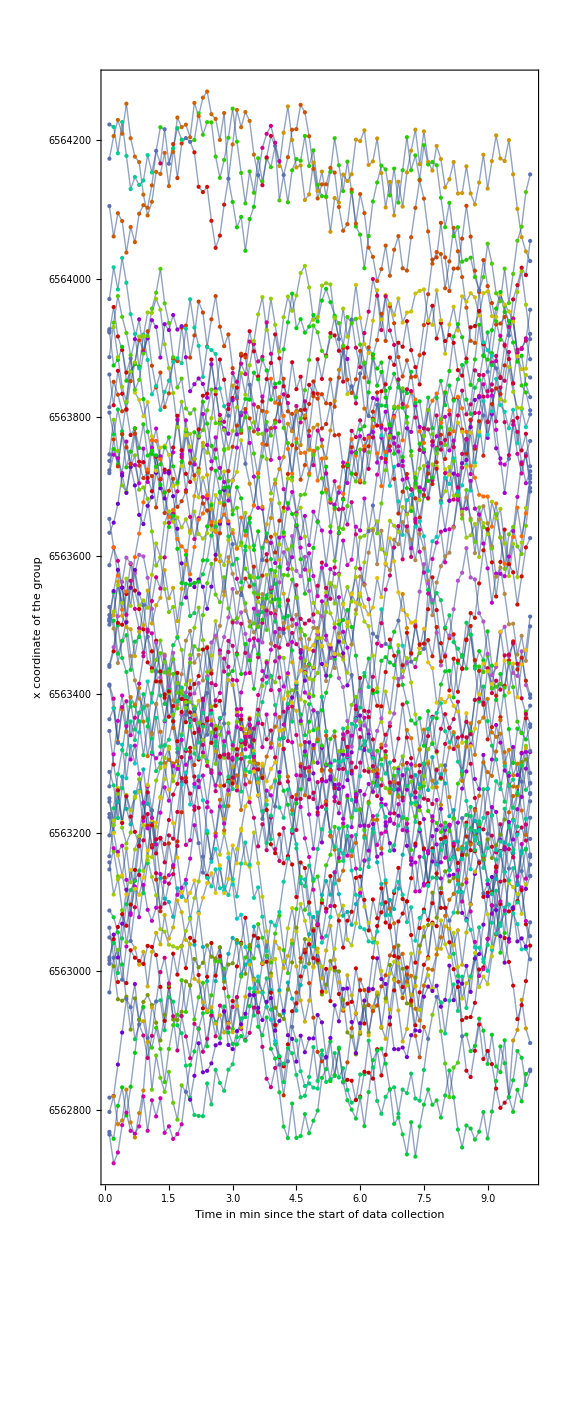

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*15&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,nullModelDataSet[[First[#][[1]],Last[#]]][[2]]}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Medium],Style["x coordinate of the group",Medium]}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```